```mathematica
验证能量守恒,观察计算误差
```

E_0= -0.0735

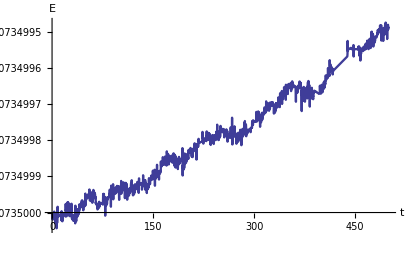

```mathematica
g=9.8;k=0.1;m=0.02;L=1;tm=500;
xinitial={0,3.5};yinitial={-L,0};
equs={x''[t]==-k/m x[t] (1-L/(√(x[t]^2+y[t]^2))),
y''[t]==-k/m y[t] (1-L/(√(x[t]^2+y[t]^2)))-g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
energy[t_]:=m (x'[t]^2+y'[t]^2)/2+m g y[t]+
k (√(x[t]^2+y[t]^2)-L)^2/2;
Print["E_0= ",m 3.5^2/2-m g L]
Plot[energy[t],{t,0,tm},PlotRange->All,
AxesLabel->{"t","E"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,k,m,L,tm,equs,s,x,y,energy]
```

```mathematica
验证能量守恒,观察计算误差——高精度计算
```

E0 = -0.0735

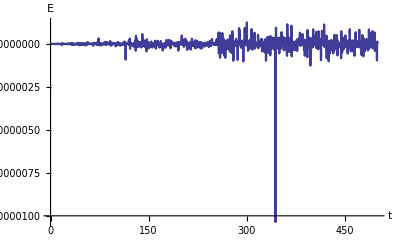

```mathematica
g=98/10;k=1/10;m=1/50;L=1;tm=500;
xinitial={0,7/2};yinitial={-L,0};
equs={x''[t]==-k/m*x[t]*(1-L/(√(x[t]^2+y[t]^2))),
y''[t]==-k/m*y[t]*(1-L/(√(x[t]^2+y[t]^2)))-g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},
MaxSteps->∞,WorkingPrecision->40];
{x,y}={x,y}/.s[[1]];
energy[t_]:=m (x'[t]^2+y'[t]^2)/2+m g y[t]+
k (√(x[t]^2+y[t]^2)-L)^2/2;
Print["E0 = ",m 3.5^2/2-m g L]
Plot[energy[t],{t,0,tm},PlotRange->All,PlotPoints->1000,AxesLabel->{"t","E"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,equs,s,x,y,energy]
```